```mathematica
SetDirectory[NotebookDirectory[]];
input=Import["uv.obj","GraphicsComplex"];
v=Part[input,1];
f=Flatten[Cases[input,Triangle[x_]->x,Infinity],1];
```

```mathematica
BoundaryLoop[f_]:=Module[{edgs,boundaryEdges,graph},
  edgs=Flatten[Map[  {
   {Part[#,1],Part[#,2]},
   {Part[#,2],Part[#,3]},
   {Part[#,3],Part[#,1]},
   {Part[#,2],Part[#,1]},
   {Part[#,3],Part[#,2]},
  {Part[#,1],Part[#,3]}
  }&,f],1];

boundaryEdges=DirectedEdge@@@Part[Select[Tally[edgs],Part[#,2]==1&],;;,1];
Part[FindHamiltonianCycle[boundaryEdges],1,;;,1]
];
```

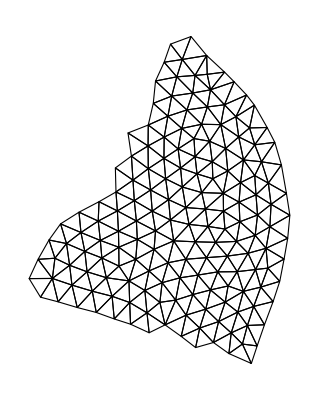

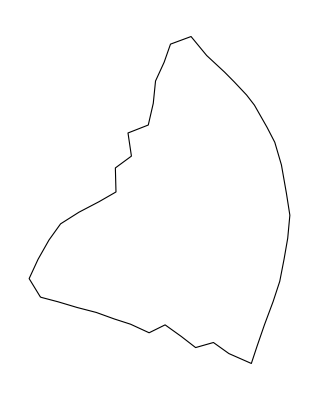

```mathematica
v2d=Part[v,;;,;;2];
loop=Part[v2d,BoundaryLoop[f]];
gr=Graphics[{
FaceForm[],
EdgeForm[Black],
GraphicsComplex[v2d,Polygon[f]]
}]
gr2=Graphics[{
FaceForm[],
EdgeForm[Black],
Polygon[loop]
}]
Export["mesh.pdf",gr,ImageSize->Full];
Export["boundary.pdf",gr2,ImageSize->Full];
```